```mathematica
Mac
f = Import["/Users/newlocaluser/Documents/MP2/Data/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["/Users/newlocaluser/Documents/MP2/Data/David Data/bci.traits.csv"];
```

```mathematica
Windows

f=Import["C:/Users/Joel/Documents/CoMPLEX/MP2/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["C:/Users/Joel/Documents/CoMPLEX/MP2/bci.traits.csv"];
```

Windows

```mathematica
bciAdultNormCrossOmegas10 = Flatten[Values[Select[f,Keys[#]=="bciAdultNormCrossOmegas10"&]],1];
index14110 = Flatten[Values[Select[f,Keys[#]=="index141_10"&]]];
```

```mathematica
B=MapThread[If[#2,MapThread[If[#2,#1,0]&,{#1,index14110}],ConstantArray[0,Length[#1]]]&,{bciAdultNormCrossOmegas10,index14110}];
```

2.75

```mathematica
adjacencyThreshold = 2.9;
Manipulate[
A = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
W = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];

An = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1<-adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
Wn = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1< -adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];
gn = Graph[An,DirectedEdges->True,EdgeWeight->Abs[Wn]];
gp =Graph[A,DirectedEdges->True,EdgeWeight->W];
g = Graph[Join[An,A],DirectedEdges->True,EdgeWeight->Join[Wn,W]];
{gp,gn,g}
,{adjacencyThreshold,2.75},ControlType->InputField]
```

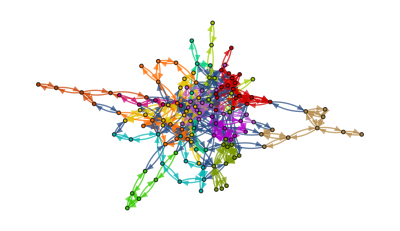

-Graphics-

```mathematica
communities = FindGraphCommunities[gp,Method->"Modularity"];
HighlightGraph[g,Map[Subgraph[g,#]&,communities]]
CommunityGraphPlot[g,communities]
```

```mathematica
ValidData[var_] := Not[MemberQ[Map[NumberQ[#]&,var],False]]
```

```mathematica
If[ValidData[{1,2,3}],1,0]
```

1

```mathematica
ReducedData = DimensionReduce[DeleteCases[Map[If[ValidData[Take[#,-3]],Take[#,{6,25}],Invalid]&,bciTraits],Invalid],3];
```

```mathematica
Graphics3D[Map[Point[#]&,ReducedData],Axes->True]
```

-Graphics3D-